```mathematica
V = {10, 5};
W = {2, 3};
Y = {1, 2};
numQ = Length[V] + Length[Y];
gamma = Max[V]+1;
(*C = 3*)
```

```mathematica
sigmaI = {{1,0},{0,1}};
sigmaX = {{0, 1}, {1,0}};
sigmaBin = {{0, 0}, {0, 1}};
```

```mathematica
H0 = KroneckerProduct[sigmaX, sigmaI, sigmaI, sigmaI]+ KroneckerProduct[sigmaI, sigmaX, sigmaI, sigmaI]+KroneckerProduct[sigmaI, sigmaI, sigmaX, sigmaI]+KroneckerProduct[sigmaI, sigmaI, sigmaI, sigmaX];
```

```mathematica
H0
```

{{0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,1,0,0,0,0,1,0,0,0,1,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,1,0,0,0},{0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0},{0,0,1,0,1,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0},{0,1,0,0,0,0,0,0,1,0,0,1,0,1,0,0},{0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,0},{0,0,0,1,0,0,0,0,0,1,1,0,0,0,0,1},{0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0}}

```mathematica
Eigensystem[H0]
```

{{-4,4,-2,-2,-2,-2,2,2,2,2,0,0,0,0,0,0},{{1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{-1,0,0,1,0,1,1,-2,2,-1,-1,0,-1,0,0,1},{0,-1,0,1,0,1,0,-1,1,0,-1,0,-1,0,1,0},{0,0,-1,1,0,0,1,-1,1,-1,0,0,-1,1,0,0},{0,0,0,0,-1,1,1,-1,1,-1,-1,1,0,0,0,0},{-1,0,0,1,0,1,1,2,-2,-1,-1,0,-1,0,0,1},{0,-1,0,-1,0,-1,0,-1,1,0,1,0,1,0,1,0},{0,0,-1,-1,0,0,-1,-1,1,1,0,0,1,1,0,0},{0,0,0,0,-1,-1,-1,-1,1,1,1,1,0,0,0,0},{1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,1},{0,1,0,0,0,0,0,-1,-1,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,-1,-1,0,0,0,0,1,0,0},{0,0,0,1,0,0,-1,0,0,-1,0,0,1,0,0,0},{0,0,0,0,1,0,0,-1,-1,0,0,1,0,0,0,0},{0,0,0,0,0,1,-1,0,0,-1,1,0,0,0,0,0}}}

```mathematica
KroneckerProduct[{{1},{-1}},{{1},{-1}},{{1},{-1}},{{1},{-1}}]
```

{{1},{-1},{-1},{1},{-1},{1},{1},{-1},{-1},{1},{1},{-1},{1},{-1},{-1},{1}}

```mathematica
Hp=- (V[[1]]KroneckerProduct[sigmaBin, sigmaI, sigmaI, sigmaI] + V[[2]]KroneckerProduct[sigmaI, sigmaBin, sigmaI, sigmaI]) + gamma((W[[1]]KroneckerProduct[sigmaBin, sigmaI, sigmaI, sigmaI] + W[[2]]KroneckerProduct[sigmaI, sigmaBin, sigmaI, sigmaI]) - (Y[[1]]KroneckerProduct[sigmaI, sigmaI, sigmaBin, sigmaI] + Y[[2]]KroneckerProduct[sigmaI, sigmaI, sigmaI, sigmaBin])  )^2 ;
```

```mathematica
MatrixForm[Hp]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 44 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 99 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 94 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 39 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 34 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -10 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 260 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 84 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 161 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 29)

```mathematica
-15 + 11*(5-0)^2
```

260

```mathematica
H[t_]:= (1- t/T)H0 + (t/T)Hp;
```

```mathematica
H[0]==H0
```

True

```mathematica
H[T] == Hp
```

True

```mathematica
intH = Integrate[H[t],{t, 0, T}];
U = MatrixExp[-I intH];
```

```mathematica
T = 10
```

10

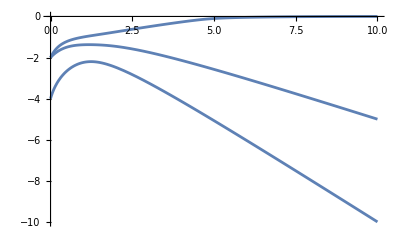

```mathematica
Plot[Sort[Eigenvalues[H[t]]][[{1,2,3}]], {t, 0, 10}]
```

```mathematica
Eigensystem[Hp]
```

{{260,161,99,94,84,44,39,34,29,11,-10,6,-5,1,1,0},{{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Eigensystem[H0]
```

{{-4,4,-2,-2,-2,-2,2,2,2,2,0,0,0,0,0,0},{{1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{-1,0,0,1,0,1,1,-2,2,-1,-1,0,-1,0,0,1},{0,-1,0,1,0,1,0,-1,1,0,-1,0,-1,0,1,0},{0,0,-1,1,0,0,1,-1,1,-1,0,0,-1,1,0,0},{0,0,0,0,-1,1,1,-1,1,-1,-1,1,0,0,0,0},{-1,0,0,1,0,1,1,2,-2,-1,-1,0,-1,0,0,1},{0,-1,0,-1,0,-1,0,-1,1,0,1,0,1,0,1,0},{0,0,-1,-1,0,0,-1,-1,1,1,0,0,1,1,0,0},{0,0,0,0,-1,-1,-1,-1,1,1,1,1,0,0,0,0},{1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,1},{0,1,0,0,0,0,0,-1,-1,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,-1,-1,0,0,0,0,1,0,0},{0,0,0,1,0,0,-1,0,0,-1,0,0,1,0,0,0},{0,0,0,0,1,0,0,-1,-1,0,0,1,0,0,0,0},{0,0,0,0,0,1,-1,0,0,-1,1,0,0,0,0,0}}}

```mathematica
PsiInitial =1 / Sqrt[16] * {1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,1};
PsiFinal = {0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0};
```

```mathematica
PsiAnnealed = U . Transpose[PsiInitial]
```

{1-ⅇ^(-5 ⅈ),-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-220 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-55 ⅈ)/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(-495 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-470 ⅈ)/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(-30 ⅈ)/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(-195 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(25 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-170 ⅈ)/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(50 ⅈ)/4,3/4-(3 ⅇ^(-5 ⅈ))/4,-3/4+(3 ⅇ^(-5 ⅈ))/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(-1300 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-420 ⅈ)/4,-3/4+ⅇ^(-5 ⅈ)-ⅇ^(-805 ⅈ)/4,3/4-ⅇ^(-5 ⅈ)+ⅇ^(-145 ⅈ)/4}

```mathematica
ConjugateTranspose[PsiInitial] . PsiInitial
```

1

```mathematica
FullSimplify[ConjugateTranspose[U] . U]
```

$Aborted